```mathematica
SetDirectory@NotebookDirectory[];
Collect[(a+b Sqrt[-2])^3//Expand,Sqrt[2]]
```

a^3-6 a b^2+√2 (3 ⅈ a^2 b-2 ⅈ b^3)

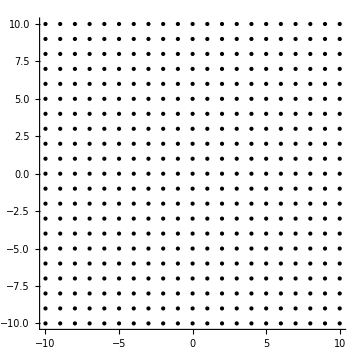
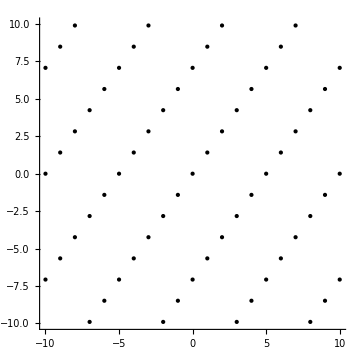
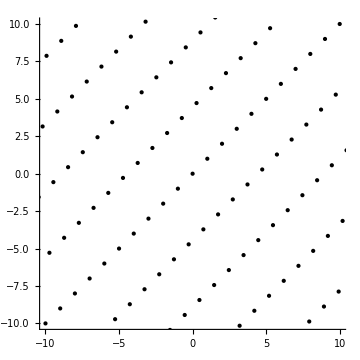

lattices.jpg

```mathematica
bound=10;
lattices={{{1,0},{0,1}},{{1,Sqrt[2]},{0,-5Sqrt[2]}},{{1,1},{Sqrt[3],-E}}};
graphs=Graphics[{PointSize@Large,Table[Point[a#⟦1⟧+b#⟦2⟧],{a,-2bound,2bound},{b,-2bound,2bound}]},Axes->True,PlotRange->{{-bound,bound},{-bound,bound}},ImageSize->Medium]&/@lattices;
pic=Row[graphs, "                                 "];
Print@pic;
Export["lattices.jpg",pic]
```

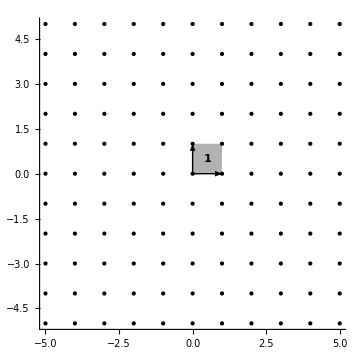
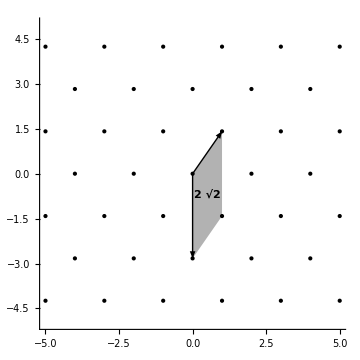

volumes.jpg

```mathematica
bound=5;
lattices={{{1,0},{0,1}},{{1,Sqrt[2]},{0,-2Sqrt[2]}}};
graphs=Graphics[{PointSize@Large,Table[Point[a#⟦1⟧+b#⟦2⟧],{a,-2bound,2bound},{b,-2bound,2bound}],Arrow[{{0,0},#⟦1⟧}],Arrow[{{0,0},#⟦2⟧}],Opacity@0.3,Polygon@{{0,0},#⟦1⟧,Total@#,#⟦2⟧},Opacity@1,Inset[Style[Abs@Det@#,Bold],Total@#/2]},Axes->True,PlotRange->{{-bound,bound},{-bound,bound}},ImageSize->Medium]&/@lattices;
pic2=Row[graphs, "                                                                 "];
Print@pic2;
Export["volumes.jpg",pic2]
```

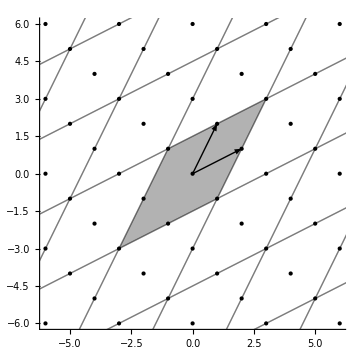

translates.jpg

```mathematica
bound=6;
lattice={{1,2},{2,1}};
latticePoints=Flatten[Table[a lattice⟦1⟧+b lattice⟦2⟧,{a,-2bound,2bound},{b,-2bound,2bound}],1];
parallelogram=Polygon@{Subtract@@lattice,Total@lattice,-Subtract@@lattice,-Total@lattice};
translates=Table[Translate[{Line[First@parallelogram~Append~First@First@parallelogram]},2l],{l,latticePoints}];
pic3=Graphics[{PointSize@Large,Point@latticePoints,Arrow[{{0,0},#}]&/@lattice,Opacity@0.3,parallelogram,translates},Axes->True,PlotRange->{{-bound,bound},{-bound,bound}},ImageSize->Medium];
Print@pic3;
Export["translates.jpg",pic3]
```

```mathematica
bound=5;
Emphasize[t_]:=Style[t,Bold,Large,Italic];
MyPlot[f_]:=Plot[f,{x,-bound,bound},PlotRange->{{-bound,bound},{-bound,bound}},ImageSize->Medium];
line=Show[MyPlot[-x],Graphics@Inset[Emphasize@"x+y=0",{-2,4}]];
hyperbola=Show[MyPlot[1/x],MyPlot[-1/x],Graphics@Inset[Emphasize@"xy=±1",{2,2}]];
arrow=Graphics[{Inset[Emphasize@"h",{0,0.6}],Arrow@BSplineCurve[{{-1,0},{0,1},{1,0}}]},ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
pic4=GraphicsRow[{line,arrow, hyperbola}];
Print@pic4
```

-Graphics-